# Multicellular Model

```mathematica
Clear["Global`*"];
```

## Deterministic evolution in the thermodynamic limit

Goal : try to study the equation for (p, Θ) in the thermodynamic limit by approximating it as a deterministic equation.

Note: requires MatLink to run (for calculating fN and gN). Alternative: run code in MATLAB and copy numbers to here.

### Define key quantities

References in EO_SuppInfo_170403_FINAL.pdf
μ_off,μ_on: eq. S47, p. 25
σ=σ_off=σ_on: eq. S48, p. 25
P_(off→ off), P_(on→ on): eq. S40, p. 24
⟨y_-⟩, ⟨y_+⟩:  eq. S52 (mean of binomial), p. 26
⟨⟨Y_-⟩⟩, ⟨⟨Y_+⟩⟩: eq. S97a, S99a, p. 46 
ϕ, Z_on, Z_off: also p. 45-46

```mathematica
μon[p_,i_]:= fN (Con*p+1-p+(Con-1)(1-p)*i);
μoff[p_,i_]:= fN (Con*p+1-p-(Con-1)p*i); 
σ[p_]:= (Con-1)Sqrt[gN p (1-p)];

Ponon[p_,i_] := 1/2*(1-Erf[(K-Con-μon[p,i])/(Sqrt[2] σ[p])]);Poffoff[p_,i_]:= 1/2*(1+Erf[(K-1-μoff[p,i])/(Sqrt[2] σ[p])]);
yp[p_,i_]:= (1-p)*(1-Poffoff[p,i]);
ym[p_,i_]:= p*(1-Ponon[p,i]);
ϕ[ξ_]:= 1/Sqrt[2π] Exp[-1/2 ξ^2];
Zoff[p_,i_]:=(K-1-μoff[p,i])/σ[p];
Zon[p_,i_]:=(K-Con-μon[p,i])/σ[p];
Yp[p_,i_]:= μoff[p,i]+σ[p]*ϕ[Zoff[p,i]]/(1-Poffoff[p,i]);
Ym[p_,i_]:= μon[p,i]-σ[p]*ϕ[Zon[p,i]]/(1-Ponon[p,i]);
```

#### Define differential equation

```mathematica
Δp[p_,i_]:= yp[p,i] - ym[p,i];
ΔΘ[p_,i_]:= 8/(n (Con-1))(yp[p,i]*Yp[p,i]-ym[p,i]*Ym[p,i])+4fN ((Δp[p,i])^2-(Con-1)/(Con+1)Δp[p,i]);
Print["Δp = ",Δp[p,i]];
Print["ΔΘ = ",ΔΘ[p,i]];
```

Δp = -p (1+1/2 (-1+Erf[(-Con+K-fN (1+(-1+Con) i (1-p)-p+Con p))/(√2 (-1+Con) √(gN (1-p) p))]))+(1-p) (1+1/2 (-1-Erf[(-1+K-fN (1-p+Con p-(-1+Con) i p))/(√2 (-1+Con) √(gN (1-p) p))]))

ΔΘ = 4 fN (-1/(1+Con)(-1+Con) (-p (1+1/2 (-1+Erf[(-Con+K-fN (1+(-1+Con) i (1-p)-p+Con p))/(√2 (-1+Con) √(gN (1-p) p))]))+(1-p) (1+1/2 (-1-Erf[(-1+K-fN (1-p+Con p-(-1+Con) i p))/(√2 (-1+Con) √(gN (1-p) p))])))+(-p (1+1/2 (-1+Erf[(-Con+K-fN (1+(-1+Con) i (1-p)-p+Con p))/(√2 (-1+Con) √(gN (1-p) p))]))+(1-p) (1+1/2 (-1-Erf[(-1+K-fN (1-p+Con p-(-1+Con) i p))/(√2 (-1+Con) √(gN (1-p) p))])))^2)+1/((-1+Con) n)8 (-p (fN (1+(-1+Con) i (1-p)-p+Con p)-((-1+Con) ⅇ^(-(-Con+K-fN (1+(-1+Con) i (1-p)-p+Con p))^2/(2 (-1+Con)^2 gN (1-p) p)) √(gN (1-p) p))/(√(2 π) (1+1/2 (-1+Erf[(-Con+K-fN (1+(-1+Con) i (1-p)-p+Con p))/(√2 (-1+Con) √(gN (1-p) p))])))) (1+1/2 (-1+Erf[(-Con+K-fN (1+(-1+Con) i (1-p)-p+Con p))/(√2 (-1+Con) √(gN (1-p) p))]))+(1-p) (fN (1-p+Con p-(-1+Con) i p)+((-1+Con) ⅇ^(-(-1+K-fN (1-p+Con p-(-1+Con) i p))^2/(2 (-1+Con)^2 gN (1-p) p)) √(gN (1-p) p))/(√(2 π) (1+1/2 (-1-Erf[(-1+K-fN (1-p+Con p-(-1+Con) i p))/(√2 (-1+Con) √(gN (1-p) p))])))) (1+1/2 (-1-Erf[(-1+K-fN (1-p+Con p-(-1+Con) i p))/(√2 (-1+Con) √(gN (1-p) p))])))

### Specify system parameters

Calculate f_N and g_N for different a_0 and N directly from MATLAB code.

```mathematica
gridsize=50;
n=gridsize^2;
a0=1.5;

Con = 14;
K=20;
```

```mathematica
Needs["MATLink`"];
OpenMATLAB[];
```

Set directory

```mathematica
dir = "H:\\My Documents\\Multicellular automaton\\";
MEvaluate[StringJoin["cd('",dir,"');"]];
MEvaluate["cd"]
```

H:\My Documents\Multicellular automaton

```mathematica
MEvaluate[StringJoin["
x1 = ",ToString[gridsize],";
x2 = ",ToString[a0],";
[a,b] = fN_calculation(x1,x2);
"]
]
fN = MGet["a"];
gN = MGet["b"];
Print["fN = ", fN, ", gN = ", gN]
```

fN = 0.518493, gN = 0.0235994

Close MATLAB

```mathematica
DisconnectEngine[]
```

Convert result from (p, Θ) to (p,I)

### Numerically solve differential equation

Parameters (initial conditions)

```mathematica
tmax = 100; 
nruns = 20;

pini = 0.1; (*initial p*)
std = 0.05;(*standard deviation for random value of I(t=0) *)
Iini = RandomVariate[NormalDistribution[0,std]]; 
Θini =Iini*4pini (1-pini) fN+(2pini-1)^2 fN;
```

Test whether chosen Θ_ini seems realistic:

```mathematica
Ilist = RandomVariate[NormalDistribution[0,std],100]; 
Θlist = Ilist *4pini (1-pini) fN+(2pini-1)^2 fN;
ListPlot[Ilist *4pini (1-pini) fN+(2pini-1)^2 fN, PlotMarkers-> "x"]
```

-Graphics-

```mathematica
i[t_]:= (Θ[t]-(2p[t]-1)^2 fN)/(4p[t] (1-p[t]) fN);
sol=ConstantArray[0,nruns];
Do[
sol[[k]]=First@NDSolve[{p'[t]==Δp[p[t],i[t]], Θ'[t]== ΔΘ[p[t],i[t]], p[0]==pini, Θ[0]==Θlist[[k]]}, {p[t], Θ[t]}, {t,0,tmax}, MaxStepSize-> tmax/100000],
{k,nruns}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve :: ndnum will be suppressed during this calculation.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[p[0] == 0.1`Θ[0] == 0.3413347684102837` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[p[0] == 0.1`Θ[0] == 0.33236446728085683` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[p[0] == 0.1`Θ[0] == 0.33096740666558505` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics-

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[p[0] == 0.1`Θ[0] == 0.3413347684102837` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[p[0] == 0.1`Θ[0] == 0.33236446728085683` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[p[0] == 0.1`Θ[0] == 0.33096740666558505` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[p[0] == 0.1`Θ[0] == 0.3413347684102837` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[p[0] == 0.1`Θ[0] == 0.33236446728085683` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[p[0] == 0.1`Θ[0] == 0.33096740666558505` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[p[0] == 0.1`Θ[0] == 0.3413347684102837` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[p[0] == 0.1`Θ[0] == 0.33236446728085683` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[p[0] == 0.1`Θ[0] == 0.33096740666558505` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

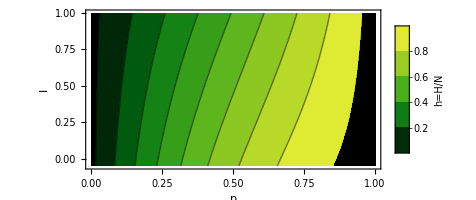

```mathematica
fig1=Plot[{p[t]/.sol, i[t]/.sol},{t,0,tmax}, PlotLegends-> {"p(t)", "I(t)"},Frame-> True, FrameLabel-> {"I(t)","p(t)"}]
energy[p_,i_]:=(-(Con-1)/2(1+4 fN p(1-p)i+(2p-1)^2 fN) - (2p-1) ((Con +1)/2(1+fN) -K) ); 
p1=ContourPlot[energy[p,i], {p,0,1},{i,-0.05,1},ColorFunction->"AvocadoColors",PlotLegends->BarLegend["AvocadoColors",{Automatic,8},LegendLabel->Placed["h=H/N",Right,Rotate[#,270Degree]&] ]];
p2=ParametricPlot[{ p[t], i[t]}/.sol,{t,0,tmax}, PlotRange-> {{0,1},{-0.05,1}},  PlotStyle-> Red];
p3a=ListPlot[{{p[t],i[t]} /.sol/.{t-> 0}}, PlotStyle->Green, PlotMarkers-> "o"];
p3b=ListPlot[{{p[t],i[t]} /.sol/.{t-> tmax}}, PlotStyle-> Black, PlotMarkers-> "x"];
fig2=Show[p1,p2,p3a,p3b,AspectRatio->0.5,Frame-> True, FrameLabel-> {"p","I"}]
```

```mathematica
h[t_]:=energy[p0,i0] /. {p0-> (p[t]/.sol), i0-> (i[t]/.sol)}; 

fig3=Plot[h[t],{t,0,tmax},PlotRange-> All, PlotStyle-> Red, Frame-> True, FrameLabel-> {"t", "h(t)"}]
```

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[p[0] == 0.1`Θ[0] == 0.3413347684102837` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[p[0] == 0.1`Θ[0] == 0.33236446728085683` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[p[0] == 0.1`Θ[0] == 0.33096740666558505` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics-

### Export graphs

```mathematica
dir=FileNameJoin[{NotebookDirectory[],"figures", "deterministic_mathematica"}];
SetDirectory[dir]
```

H:\My Documents\Multicellular automaton\figures\deterministic_mathematica

```mathematica
fpattern = StringJoin["N", ToString[n],"_n", StringReplace[ToString[Round[pini*n]],"."-> "p"], "_a0_", StringReplace[ToString[a0],"."-> "p"], "_Con", ToString[Con], "_K", ToString[K]]
```

N2500_n1250_a0_1p5_Con20_K16

```mathematica
Export[StringJoin[fpattern,"dynamics", ".pdf"],fig1]
Export[StringJoin[fpattern,"h_path", ".pdf"],fig2]
Export[StringJoin[fpattern,"allH", ".pdf"], fig3]
```

N2500_n1250_a0_1p5_Con20_K16dynamics.pdf

N2500_n1250_a0_1p5_Con20_K16h_path.pdf

N2500_n1250_a0_1p5_Con20_K16allH.pdf